```mathematica
wave1=.;wave1[s_,ϕ_]:=Sin[ϕ*2π*s];
wave2=.;wave2[s_,ϕ_]:=Sin[ϕ*2π*s]+Sin[2*ϕ*2π*s];
wave3o2=.;wave3o2[s_,ϕ_]:=Sin[ϕ*2π*s]+Sin[3/2*ϕ*2π*s];
```

Frequency ϕ, lag τ

```mathematica
lagresponse[wave_,ϕ_,τ_]:=Integrate[wave[t,ϕ]*wave[t-τ,ϕ],{t,0,1/ϕ}]
```

```mathematica
lagresponse[wave1,1,τ]
```

1/2 Cos[2 π τ]

```mathematica
lagresponse[wave2,1,τ]
```

```mathematica
1/2 (Cos[2 π τ]+Cos[4 π τ])
```

1/2 (Cos[2 π τ]+Cos[4 π τ])

```mathematica
lagresponse[wave3o2,1,τ]
```

(5 π Cos[2 π τ]+5 π Cos[3 π τ]-12 Sin[2 π τ]+8 Sin[3 π τ])/(10 π)

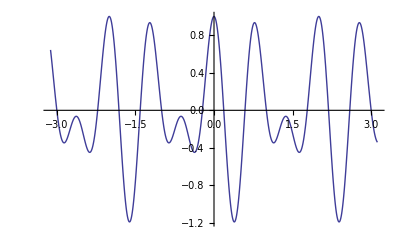

```mathematica
Plot[(5 π Cos[2 π τ]+5 π Cos[3 π τ]-12 Sin[2 π τ]+8 Sin[3 π τ])/(10 π),{τ,-3.12,3.12}]
```

```mathematica
lagresponse[wave3o2,1,τ]
```

(5 π Cos[2 π τ]+5 π Cos[3 π τ]-12 Sin[2 π τ]+8 Sin[3 π τ])/(10 π)